# More Coupled Oscillators

## Two weakly coupled oscillators

```mathematica
Clear["`*"]
```

Set up the Lagrangian and get the equations of motion.

```mathematica
L=1/2 m x1dot^2+1/2 m x2dot^2-1/2 k x1^2-1/2 k2 (x2-x1)^2-1/2 k x2^2;
rule={x1->x1[t],x1dot->x1'[t],x2->x2[t],x2dot->x2'[t]};
p1=D[L,x1dot]/.rule
p2=D[L,x2dot]/.rule
dLdx1=D[L,x1]/.rule
dLdx2=D[L,x2]/.rule
```

m x1'[t]

m x2'[t]

-k x1[t]+k2 (-x1[t]+x2[t])

-k x2[t]-k2 (-x1[t]+x2[t])

```mathematica
eq1=dLdx1==D[p1,t]
eq2=dLdx2==D[p2,t]
```

-k x1[t]+k2 (-x1[t]+x2[t])==m x1''[t]

-k x2[t]-k2 (-x1[t]+x2[t])==m x2''[t]

Solve the equations with initial conditions corresponding to each normal mode as well as arbitrary initial conditions.

```mathematica
m=1;
k=1;
k2=0.05;
sol3=DSolve[{eq1,eq2,x1[0]==0.05,x2[0]==0.0,x1'[0]==0,x2'[0]==0},{x1[t],x2[t]},t]
```

{{x1[t]→(3.46945×10^-19+0.025 ⅈ) ((0.-1. ⅈ) Cos[1. t]+(2.77556×10^-17-1. ⅈ) Cos[1.04881 t]+(2.12816×10^-32+6.86942×10^-16 ⅈ) Sin[1. t]+(5.53119×10^-32-6.54974×10^-16 ⅈ) Sin[1.04881 t]),x2[t]→(0.025+3.46945×10^-19 ⅈ) ((1.+0. ⅈ) Cos[1. t]-(1.-5.77779×10^-33 ⅈ) Cos[1.04881 t]+(1.2837×10^-15+4.38148×10^-32 ⅈ) Sin[1. t]-(1.22396×10^-15+2.92364×10^-32 ⅈ) Sin[1.04881 t])}}

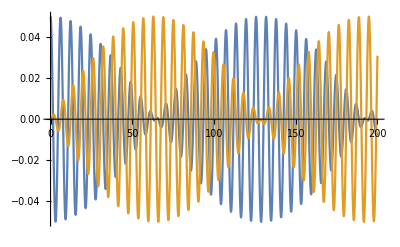

```mathematica
Plot[{x1[t]/.sol3,x2[t]/.sol3},{t,0,200}]
```

```mathematica
X13[t_]=Chop[x1[t]/.sol3][[1]];
X23[t_]=Chop[x2[t]/.sol3][[1]];

Manipulate[Graphics[{Black,Line[{{-0.17,0},{0.17,0}}],Line[{{0,-0.02},{0,+0.02}}],Gray,Rectangle[{X23[t]+0.06-0.005,-0.005},{X23[t]+0.06+0.005,0.005}],Gray,Rectangle[{X13[t]-0.06-0.005,-0.005},{X13[t]-0.06+0.005,0.005}]}],{t,0,200}]
```

```mathematica
Clear["`*"]
```

```mathematica
MM=m L^2 {{1,0,0},{0,1,0},{0,0,1}};MM//MatrixForm
KM={{m g L + k L^2,-k L^2,0},{-k L^2,m g L + 2 k L^2,-k L^2},{0,-k L^2, m g L + k L^2}};KM//MatrixForm
MinvK=Inverse[MM].KM;MinvK//MatrixForm
```

(L^2 m | 0 | 0
0 | L^2 m | 0
0 | 0 | L^2 m)

(k L^2+g L m | -k L^2 | 0
-k L^2 | 2 k L^2+g L m | -k L^2
0 | -k L^2 | k L^2+g L m)

((k L^2+g L m)/(L^2 m) | -k/m | 0
-k/m | (2 k L^2+g L m)/(L^2 m) | -k/m
0 | -k/m | (k L^2+g L m)/(L^2 m))

```mathematica
Simplify[Eigensystem[MinvK]]
```

{{g/L,g/L+k/m,g/L+(3 k)/m},{{1,1,1},{-1,0,1},{1,-2,1}}}